```mathematica
(* This function calculates QFIM of density matrix "mat" for variables "variables" *)
Fisher[mat_,variables_]:=(
result=Array[0&,{Length[variables],Length[variables]}];
evals=Simplify[Eigenvalues[mat]];
evecs=Eigenvectors[mat]//Simplify;
For[i=1,i≤Length[variables],i++,
For[j=1,j≤Length[variables],j++,
firstVar=variables[[i]];
secondVar=variables[[j]];
fisher1=fisher2=fisher3=0;
For[k=1,k≤Length[evals],k++,
If[evals[[k]]=!=0,
eval1=evals[[k]];
evec1=evecs[[k]];
KetEvec1=Simplify[Transpose[{evec1}]];
BraEvec1=Simplify[ConjugateTranspose[KetEvec1]];
norm1=Sqrt[(Simplify[BraEvec1.KetEvec1])[[1,1]]];
KetEvec1=Simplify[KetEvec1/norm1];
BraEvec1=Simplify[BraEvec1/norm1];
BraEvec1Prime1=D[BraEvec1,firstVar];
KetEvec1Prime1=D[KetEvec1,firstVar];
BraEvec1Prime2=D[BraEvec1,secondVar];
KetEvec1Prime2=D[KetEvec1,secondVar];

eval1Prime1=D[eval1,firstVar];
eval1Prime2=D[eval1,secondVar];

fisher1+=eval1Prime1*eval1Prime2/eval1;
fisher2+=eval1*Re[(BraEvec1Prime1.KetEvec1Prime2)[[1,1]]];
For[l=1,l≤Length[evals],l++,
If[evals[[l]]=!=0 ,
eval2=evals[[l]];
evec2=evecs[[l]];
KetEvec2=Simplify[Transpose[{evec2}]];
BraEvec2=Simplify[ConjugateTranspose[KetEvec2]];
norm2=Sqrt[(Simplify[BraEvec2.KetEvec2])[[1,1]]];
KetEvec2=Simplify[KetEvec2/norm2];
BraEvec2=Simplify[BraEvec2/norm2];
BraEvec2Prime1=D[BraEvec2,firstVar];
KetEvec2Prime1=D[KetEvec2,firstVar];
BraEvec2Prime2=D[BraEvec2,secondVar];
KetEvec2Prime2=D[KetEvec2,secondVar];
fisher3+=eval1*eval2*Re[(BraEvec1Prime1.KetEvec2)[[1,1]] *(BraEvec2.KetEvec1Prime2 )[[1,1]]]/(eval1+eval2);
];
];
];
];
Print[variables[[i]],variables[[j]]," done"];
result[[i,j]]=(fisher1+4*fisher2-8*fisher3)//Simplify;
];
];
ClearAll[i,j,k,l,fisher1,fisher2,fisher3,KetEvec1,KetEvec1Prime1,KetEvec1Prime2,KetEvec2,KetEvec2Prime1,KetEvec2Prime2,BraEvec1,BraEvec1Prime1,BraEvec1Prime2,BraEvec2,BraEvec2Prime1,BraEvec2Prime2,evecs,evec1,evec2,evals,eval1,eval1Prime1,eval2,eval1Prime2,firstVar,secondVar];
Return[result];
);
```

```mathematica
(* two Photons in mach zehnder - there are 6 distinct states *)
(* set global assumptions *)
$Assumptions={T,ϕ,γ}∈Reals&&T>=0&&T<=1;
(* Define transmission and reflection coefficients *)
t =T Exp[-I γ];
r=Sqrt[1-T^2];
(*  |ψ> =a1|200>+a2|110>+a3|020>+a4|101>+a5|011>+a6|002>  *)
a1=-(t-Exp[-I ϕ ])^2/4;
a2=I Sqrt[2](Exp[-2I ϕ ]-t^2)/4;
a3=(t+Exp[-I ϕ ])^2/4;
a4=-r(t-Exp[-I ϕ ])/2;
a5=I r(t+Exp[-I ϕ ])/2;
a6=-r^2/2;

ψ={{a1},{a2},{a3},{a4},{a5},{a6}};
ψ//MatrixForm
ρ=ψ.ConjugateTranspose[ψ]//Simplify;
Norm[ψ]//FullSimplify
```

(-1/4 (-ⅇ^(-ⅈ ϕ)+ⅇ^(-ⅈ γ) T)^2
(ⅈ (ⅇ^(-2 ⅈ ϕ)-ⅇ^(-2 ⅈ γ) T^2))/(2 √2)
1/4 (ⅇ^(-ⅈ ϕ)+ⅇ^(-ⅈ γ) T)^2
-1/2 (-ⅇ^(-ⅈ ϕ)+ⅇ^(-ⅈ γ) T) √(1-T^2)
1/2 ⅈ (ⅇ^(-ⅈ ϕ)+ⅇ^(-ⅈ γ) T) √(1-T^2)
1/2 (-1+T^2))

1

```mathematica
(* Tracing over dissipated photons in path |w> *)
For[i=1,i≤3,i++,
For[j=4,j≤6,j++,
ρ[[i,j]]=ρ[[j,i]]=0
]];
ρ[[6,5]]=ρ[[6,4]]=ρ[[5,6]]=ρ[[4,6]]=0;
ρ//MatrixForm
```

(1/16 (1-ⅇ^(-ⅈ (γ-ϕ)) T-ⅇ^(ⅈ (γ-ϕ)) T+T^2)^2 | (ⅈ (ⅇ^(-ⅈ ϕ)-ⅇ^(-ⅈ γ) T)^2 (ⅇ^(2 ⅈ ϕ)-ⅇ^(2 ⅈ γ) T^2))/(8 √2) | -1/16 (ⅇ^(-ⅈ ϕ)-ⅇ^(-ⅈ γ) T)^2 (ⅇ^(ⅈ ϕ)+ⅇ^(ⅈ γ) T)^2 | 0 | 0 | 0
-(ⅈ (ⅇ^(ⅈ ϕ)-ⅇ^(ⅈ γ) T)^2 (ⅇ^(-2 ⅈ ϕ)-ⅇ^(-2 ⅈ γ) T^2))/(8 √2) | 1/8 (ⅇ^(-2 ⅈ ϕ)-ⅇ^(-2 ⅈ γ) T^2) (ⅇ^(2 ⅈ ϕ)-ⅇ^(2 ⅈ γ) T^2) | (ⅈ (ⅇ^(ⅈ ϕ)+ⅇ^(ⅈ γ) T)^2 (ⅇ^(-2 ⅈ ϕ)-ⅇ^(-2 ⅈ γ) T^2))/(8 √2) | 0 | 0 | 0
-1/16 (ⅇ^(-ⅈ ϕ)+ⅇ^(-ⅈ γ) T)^2 (ⅇ^(ⅈ ϕ)-ⅇ^(ⅈ γ) T)^2 | -(ⅈ (ⅇ^(-ⅈ ϕ)+ⅇ^(-ⅈ γ) T)^2 (ⅇ^(2 ⅈ ϕ)-ⅇ^(2 ⅈ γ) T^2))/(8 √2) | 1/16 (ⅇ^(-ⅈ ϕ)+ⅇ^(-ⅈ γ) T)^2 (ⅇ^(ⅈ ϕ)+ⅇ^(ⅈ γ) T)^2 | 0 | 0 | 0
0 | 0 | 0 | 1/4 ⅇ^(-ⅈ (γ+ϕ)) (-ⅇ^(ⅈ ϕ)+ⅇ^(ⅈ γ) T) (ⅇ^(ⅈ γ)-ⅇ^(ⅈ ϕ) T) (-1+T^2) | 1/4 ⅈ ⅇ^(-ⅈ (γ+ϕ)) (ⅇ^(ⅈ ϕ)+ⅇ^(ⅈ γ) T) (ⅇ^(ⅈ γ)-ⅇ^(ⅈ ϕ) T) (-1+T^2) | 0
0 | 0 | 0 | 1/4 ⅈ ⅇ^(-ⅈ (γ+ϕ)) (-ⅇ^(ⅈ ϕ)+ⅇ^(ⅈ γ) T) (ⅇ^(ⅈ γ)+ⅇ^(ⅈ ϕ) T) (-1+T^2) | -1/4 ⅇ^(-ⅈ (γ+ϕ)) (ⅇ^(ⅈ ϕ)+ⅇ^(ⅈ γ) T) (ⅇ^(ⅈ γ)+ⅇ^(ⅈ ϕ) T) (-1+T^2) | 0
0 | 0 | 0 | 0 | 0 | 1/4 (-1+T^2)^2)

```mathematica
(* Calculate Quantum Fisher Information Matrix *)
fisher=Fisher[ρ,{ϕ,γ,T}];
```

ϕϕ done

ϕγ done

ϕT done

γϕ done

γγ done

γT done

Tϕ done

Tγ done

TT done

```mathematica
(* Simplify eqautions obtained for QFIM *)
fisher=fisher//ComplexExpand//Simplify;
fisher//MatrixForm
```

((4 T^2)/(1+T^2) | -(4 T^2)/(1+T^2) | 0
-(4 T^2)/(1+T^2) | (4 T^2)/(1+T^2) | 0
0 | 0 | -4/(-1+T^2))

```mathematica
(* Calulate determinant of QFIM *)
Det[fisher]//Simplify
```

0

```mathematica
(* Calculate variance and covariance for objects characteristics *)
reducedfisher={{fisher[[2,2]],fisher[[2,3]]},{fisher[[3,2]],fisher[[3,3]]}};
cov=Inverse[reducedfisher//Simplify]//Simplify;
cov//MatrixForm
```

(1/4 (1+1/T^2) | 0
0 | 1/4 (1-T^2))

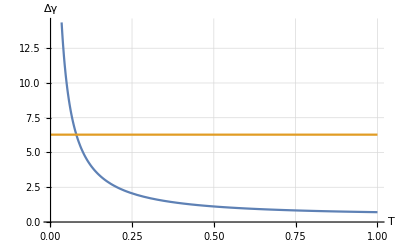

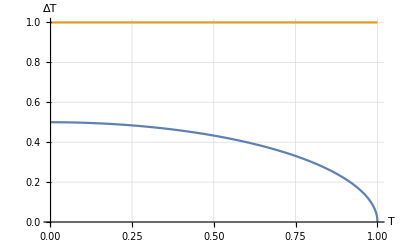

```mathematica
p1=Plot[{Sqrt[cov[[1,1]]],2*Pi},{T,0.001,1},AxesLabel->{"T","Δγ"},GridLines->Automatic]
p2=Plot[{Sqrt[cov[[2,2]]],1},{T,0.001,1},AxesLabel->{"T","ΔT"},GridLines->Automatic]
Export["two-photon-dg.png",p1,ImageResolution->300];
Export["two-photon-dt.png",p2,ImageResolution->300];
```